## Begin Package

-Graphics-

-Graphics-

```mathematica
BeginPackage["ASTRAInterpreter`"]
```

ASTRAInterpreter`

```mathematica
Needs["h5mma`"]
```

```mathematica
ASTRAColumnsXemit = {{"z", Quantity["Meters"],Number}, {"t", Quantity["ns"],Number}, {"xavr", Quantity["mm"],Number}, {"xrms", Quantity["mm"],Number}, {"xprms", Quantity["mrad"],Number}, {"ϵxnorm", Quantity[IndependentUnit["π"]] Quantity["mm"] Quantity["mrad"],Number}, {"xxpavr", Quantity["mm"] Quantity["mrad"],Number}};
```

```mathematica
ASTRAColumnsYemit={{"z",Quantity["Meters"],Number},{"t",Quantity["ns"],Number},{"yavr",Quantity["mm"],Number},{"yrms",Quantity["mm"],Number},{"yprms",Quantity["mrad"],Number},{"ϵynorm",Quantity[IndependentUnit["π"]] Quantity["mm"]Quantity["mrad"],Number},{"yypavr",Quantity["mm"]Quantity["mrad"],Number}};
```

```mathematica
ASTRAColumnsZemit={{"z",Quantity["Meters"],Number},{"t",Quantity["ns"],Number},{"Ekin",Quantity["MeV"],Number},{"zrms",Quantity["mm"],Number},{"ΔErms",Quantity["keV"],Number},{"ϵznorm",Quantity[IndependentUnit["π"]] Quantity["mm"]Quantity["keV"],Number},{"zEavr",Quantity["keV"],Number}};
```

```mathematica
ASTRAColumnsParticles={{"x",Quantity["Meters"],Number},{"y",Quantity["Meters"],Number},{"z",Quantity["Meters"],Number},{"px",Quantity["eV"]/Quantity["SpeedOfLight"],Number},{"py",Quantity["eV"]/Quantity["SpeedOfLight"],Number},{"pz",Quantity["eV"]/Quantity["SpeedOfLight"],Number},{"clock",Quantity["ns"],Number},{"charge",Quantity["nC"],Number},{"index",1,Number},{"status",1,Number}};
```

```mathematica
ASTRAXemitInterpret::usage="ASTRAXemitInterpret[file] interpret the ASTRA X-Emit file into Mathematica format."
```

ASTRAXemitInterpret[file] interpret the ASTRA X-Emit file into Mathematica format.

```mathematica
ASTRAYemitInterpret::usage="ASTRAYemitInterpret[file] interpret the ASTRA Y-Emit file into Mathematica format."
```

ASTRAYemitInterpret[file] interpret the ASTRA Y-Emit file into Mathematica format.

```mathematica
ASTRAZemitInterpret::usage="ASTRAZemitInterpret[file] interpret the ASTRA Z-Emit file into Mathematica format."
```

ASTRAZemitInterpret[file] interpret the ASTRA Z-Emit file into Mathematica format.

```mathematica
ASTRAemitInterpret::usage="ASTRAemitInterpret[file] interpret the ASTRA Emit files into Mathematica format assuming the naming convention \"*[X/Y/Z]emit*\"."
```

ASTRAemitInterpret[file] interpret the ASTRA Emit files into Mathematica format assuming the naming convention "*[X/Y/Z]emit*".

```mathematica
ASTRAemitInterpretHDF5Summary::usage="ASTRAemitInterpretHDF5Summary[file] interpret the ASTRA Emit files into Mathematica format from an HDF5 ASTRA Summary file."
```

```mathematica
ASTRABeamInterpret::usage="ASTRABeamInterpret[file] interpret the ASTRA Paticle file into Mathematica format."
```

ASTRABeamInterpret[file] interpret the ASTRA Paticle file into Mathematica format.

```mathematica
unitConversionRules = {"Nanoseconds" -> "ns", "Milliradians" -> "mrad", "Millimeters" -> "mm", "Megaelectronvolts" -> "MeV", "Kiloelectronvolts" -> "keV","Nanocoulombs"->"nC","Electronvolts"->"eV","Meters"->"m"}
```

```mathematica
Begin["`Private`"]
```

ASTRAInterpreter`Private`

```mathematica
ASTRAemitInterpret::wrongFileType="Filename doesn't contain \"`1`emit\". Override with IgnoreFilename→True"
```

Filename doesn't contain "`1`emit". Override with IgnoreFilename→True

```mathematica
ASTRAImportData[file_,columns_]:=Transpose[ReadList[file,columns[[All,-1]]]]
```

```mathematica
ASTRAImportData[files_List,columns_]:=Transpose[Join[Sequence@@Block[{file=#},
ReadList[file,columns[[All,-1]]]
]&/@files]]
```

```mathematica
ASTRAColumnsAssign[columns_,data_,opts___Rule]:=Block[{prefix,postfix,units},
prefix=Global`ASTRAPrefix/.{opts}/.{Global`ASTRAPrefix->""};
postfix=Global`ASTRAPostfix/.{opts}/.{Global`ASTRAPostfix->""};
units=Global`ASTRAUnits/.{opts}/.{Global`ASTRAUnits->False};
(Clear[Evaluate[prefix<>#[[1,1]]<>postfix]];
Evaluate[Symbol@Evaluate[prefix<>#[[1,1]]<>postfix]]=If[units,#[[1,2]],1]#[[2]])&/@Transpose[{columns,data}];
]
```

```mathematica
ASTRAPrintColumns[columns_,opts___Rule]:=Block[{prefix,postfix},
prefix=Global`ASTRAPrefix/.{opts}/.{Global`ASTRAPrefix->""};
postfix=Global`ASTRAPostfix/.{opts}/.{Global`ASTRAPostfix->""};
Print[StringReplace["Columns Redefined: "<>StringJoin@@MapIndexed[If[#2[[1]]>1,", ",""]<>prefix<>#[[1]]<>postfix<>" ["<>StringJoin@@MapIndexed[If[#2[[1]]>1," ",""]<>ToString[#]&,
Replace[
If[(cases=Cases[{QuantityUnit[#[[2]]]},Times[a_,Power["SpeedOfLight",b_]]:>a<>If[Sign[b]<0,"/"]<>ToString["c"<>If[Abs[b]=!=1,"^"<>ToString[Abs[b]],""]]])==={},
QuantityUnit[#[[2]]],
cases],IndependentUnit[a_]:>a,∞]
]<>"]"&,columns],unitConversionRules]]
]
```

```mathematica
ASTRAXemitInterpret[file_String,opts___Rule]:=Block[{dataASTRAx,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
If[!StringMatchQ[file,"*Xemit*"]&&!ignorefilename,
Message[ASTRAemitInterpret::wrongFileType,"X"],
dataASTRAx=ASTRAImportData[file,ASTRAColumnsXemit];
ASTRAColumnsAssign[ASTRAColumnsXemit,dataASTRAx,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsXemit,opts]]
]
]
```

```mathematica
ASTRAXemitInterpret[{files__String},opts___Rule]:=Block[{dataASTRAx,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
If[!(And@@(StringMatchQ[#,"*Xemit*"]&/@{files}))&&!ignorefilename,
Message[ASTRAemitInterpret::wrongFileType,"X"],
dataASTRAx=ASTRAImportData[{files},ASTRAColumnsXemit];
ASTRAColumnsAssign[ASTRAColumnsXemit,dataASTRAx,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsXemit,opts]]
]
]
```

```mathematica
ASTRAXemitInterpret[data_List,opts___Rule]:=Block[{dataASTRAx,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
dataASTRAx=Transpose[Join[Sequence@@data]];
ASTRAColumnsAssign[ASTRAColumnsXemit,dataASTRAx,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsXemit,opts]]
]
```

```mathematica
ASTRAYemitInterpret[file_String,opts___Rule]:=Block[{dataASTRAy,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
If[!StringMatchQ[file,"*Yemit*"]&&!ignorefilename,
Message[ASTRAemitInterpret::wrongFileType,"Y"],
dataASTRAy=ASTRAImportData[file,ASTRAColumnsYemit];
ASTRAColumnsAssign[ASTRAColumnsYemit,dataASTRAy,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsYemit,opts]]
]
]
```

```mathematica
ASTRAYemitInterpret[data_List,opts___Rule]:=Block[{dataASTRAy,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
dataASTRAy=Transpose[Join[Sequence@@data]];
ASTRAColumnsAssign[ASTRAColumnsYemit,dataASTRAy,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsYemit,opts]]
]
```

```mathematica
ASTRAYemitInterpret[{files__String},opts___Rule]:=Block[{dataASTRAy,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
If[!(And@@(StringMatchQ[#,"*Yemit*"]&/@{files}))&&!ignorefilename,
Message[ASTRAemitInterpret::wrongFileType,"Y"],
dataASTRAy=ASTRAImportData[{files},ASTRAColumnsYemit];
ASTRAColumnsAssign[ASTRAColumnsYemit,dataASTRAy,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsYemit,opts]]
]
]
```

```mathematica
ASTRAZemitInterpret[file_String,opts___Rule]:=Block[{dataASTRAz,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
If[!StringMatchQ[file,"*Zemit*"]&&!ignorefilename,
Message[ASTRAemitInterpret::wrongFileType,"Z"],
dataASTRAz=ASTRAImportData[file,ASTRAColumnsZemit];
ASTRAColumnsAssign[ASTRAColumnsZemit,dataASTRAz,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsZemit,opts]]
]
]
```

```mathematica
ASTRAZemitInterpret[data_List,opts___Rule]:=Block[{dataASTRAz,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
dataASTRAz=Transpose[Join[Sequence@@data]];
ASTRAColumnsAssign[ASTRAColumnsZemit,dataASTRAz,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsZemit,opts]]
]
```

```mathematica
ASTRAZemitInterpret[{files__String},opts___Rule]:=Block[{dataASTRAz,verbose,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
ignorefilename=Global`IgnoreFilename/.{opts}/.{Global`IgnoreFilename->False};
If[!(And@@(StringMatchQ[#,"*Zemit*"]&/@{files}))&&!ignorefilename,
Message[ASTRAemitInterpret::wrongFileType,"Z"],
dataASTRAz=ASTRAImportData[{files},ASTRAColumnsZemit];
ASTRAColumnsAssign[ASTRAColumnsZemit,dataASTRAz,opts];
If[verbose,ASTRAPrintColumns[ASTRAColumnsZemit,opts]]
]
]
```

```mathematica
ASTRAemitInterpret[file_String,opts___Rule]:=Block[{},
ASTRAXemitInterpret[StringReplace[file,{"Yemit"->"Xemit","Zemit"->"Xemit"}],opts];
ASTRAYemitInterpret[StringReplace[file,{"Xemit"->"Yemit","Zemit"->"Yemit"}],opts];
ASTRAZemitInterpret[StringReplace[file,{"Xemit"->"Zemit","Yemit"->"Zemit"}],opts];
]
```

```mathematica
ASTRAemitInterpret[{files__String},opts___Rule]:=Block[{},
ASTRAXemitInterpret[StringReplace[{files},{"Yemit"->"Xemit","Zemit"->"Xemit"}],opts];
ASTRAYemitInterpret[StringReplace[{files},{"Xemit"->"Yemit","Zemit"->"Yemit"}],opts];
ASTRAZemitInterpret[StringReplace[{files},{"Xemit"->"Zemit","Yemit"->"Zemit"}],opts];
]
```

```mathematica
ASTRAemitInterpret[datax_List,datay_List,dataz_List,opts___Rule]:=Block[{},
ASTRAXemitInterpret[datax,opts];
ASTRAYemitInterpret[datay,opts];
ASTRAZemitInterpret[dataz,opts];
]
```

```mathematica
ASTRAemitInterpretHDF5Summary[file_String,opts___Rule]:=Block[{datax,datay,dataz},
datax=ImportHDF5[file,{"Datasets",Select[ImportHDF5[file],StringMatchQ[#,"/Xemit/*"]&]}];
datay=ImportHDF5[file,{"Datasets",Select[ImportHDF5[file],StringMatchQ[#,"/Yemit/*"]&]}];
dataz=ImportHDF5[file,{"Datasets",Select[ImportHDF5[file],StringMatchQ[#,"/Zemit/*"]&]}];
ASTRAXemitInterpret[datax,opts];
ASTRAYemitInterpret[datay,opts];
ASTRAZemitInterpret[dataz,opts];
]
```

```mathematica
ASTRAemitInterpretHDF5Summary[{files__String},opts___Rule]:=Block[{datax,datay,dataz},
datax=Join@@(ImportHDF5[#,{"Datasets",Select[ImportHDF5[#],StringMatchQ[#,"/Xemit/*"]&]}]&/@{files});
datay=Join@@(ImportHDF5[#,{"Datasets",Select[ImportHDF5[#],StringMatchQ[#,"/Yemit/*"]&]}]&/@{files});
dataz=Join@@(ImportHDF5[#,{"Datasets",Select[ImportHDF5[#],StringMatchQ[#,"/Zemit/*"]&]}]&/@{files});
ASTRAXemitInterpret[datax,opts];
ASTRAYemitInterpret[datay,opts];
ASTRAZemitInterpret[dataz,opts];
]
```

```mathematica
ASTRABeamInterpret[file_,opts___Rule]:=Block[{dataASTRAbeam,verbose,normalise,ignorefilename},
verbose=Global`ASTRAVerbose/.{opts}/.{Global`ASTRAVerbose->False};
normalise=Global`ASTRANormalise/.{opts}/.{Global`ASTRANormalise->True};
prefix=Global`ASTRAPrefix/.{opts}/.{Global`ASTRAPrefix->""};
postfix=Global`ASTRAPostfix/.{opts}/.{Global`ASTRAPostfix->""};
dataASTRAbeam=ASTRAImportData[file,ASTRAColumnsParticles];
ASTRAColumnsAssign[ASTRAColumnsParticles,dataASTRAbeam,opts];
If[normalise==True,
ToExpression["Global`"<>prefix<>"z"<>postfix<>"[[2;;-1]]=Rest[Global`"<>prefix<>"z"<>postfix<>"]+First[Global`"<>prefix<>"z"<>postfix<>"]"];
ToExpression["Global`"<>prefix<>"pz"<>postfix<>"[[2;;-1]]=Rest[Global`"<>prefix<>"pz"<>postfix<>"]+First[Global`"<>prefix<>"pz"<>postfix<>"]"]
];
If[verbose,ASTRAPrintColumns[ASTRAColumnsParticles,opts]]
]
```

```mathematica
End[]
```

ASTRAInterpreter`Private`

```mathematica
EndPackage[]
```

## Testing

```mathematica
<<ASTRAInterpret`
```

Global`Prefix::shdw: Symbol "Prefix" appears in multiple contexts {"Global`", "System`"}; definitions in context "Global`" may shadow or be shadowed by other definitions.

Global`Postfix::shdw: Symbol "Postfix" appears in multiple contexts {"Global`", "System`"}; definitions in context "Global`" may shadow or be shadowed by other definitions.

```mathematica
SetDirectory["F:\\My Documents\\Mathematica\\CLARA\\CLARAv32_PARS\\250-MC-05"]
```

F:\My Documents\Mathematica\CLARA\CLARAv32_PARS\250-MC-05

```mathematica
ASTRAXemitInterpret["020.Xemit.001",ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

```mathematica
testFunc[filename_,columns_]:=Block[{file},
file=OpenWrite[filename<>".ascii"];
WriteString[file,"SDDS1\n"];
WriteString[file,"&column name="<>StringReplace[#[[1]],{"ϵ"->"e"}]<>", symbol="<>StringReplace[#[[1]],{"ϵ"->"e"}]<>", units=\""<>StringReplace[ToString[Replace[QuantityUnit[#[[2]]],{IndependentUnit[a_]:>1(*,"Milliradians"->1*)},∞]],unitConversionRules]<>"\", type="<>(#[[3]]/.{Number->"double"})<>" &end\n"]&/@columns;
WriteString[file,"&data
    mode = \"ascii\" &end\n"];
WriteString[file,ToString[Length[ToExpression[columns[[1,1]]]]]<>"\n"];
WriteString[file,Row[Join[CForm/@#,{"\n"}]," "]]&/@Transpose[QuantityMagnitude[ToExpression[columns[[All,1]]]]];
Close[file];
ReadList["!sddsconvert -binary "<>filename<>".ascii "<>filename,Record];
]
```

```mathematica
testFunc["test.sdds",ASTRAColumnsXemit]//AbsoluteTiming
```

{0.142,Null}

```mathematica
ASTRAXemitInterpret["020.Xemit.001",ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

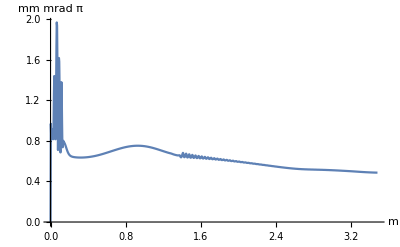

```mathematica
ListLinePlot[{Transpose[{z,ϵxnorm}]},AxesLabel->Automatic,PlotRange->All]
```

```mathematica
ASTRAYemitInterpret["020.Yemit.001",ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

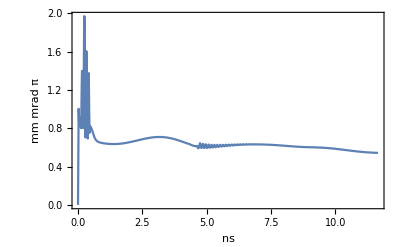

```mathematica
ListLinePlot[{Transpose[{t,ϵynorm}]},FrameLabel->Automatic,Frame->True,PlotRange->All]
```

```mathematica
ASTRAZemitInterpret["020.Zemit.001",ASTRAVerbose->True]
```

Columns Redefined: z [Meters], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

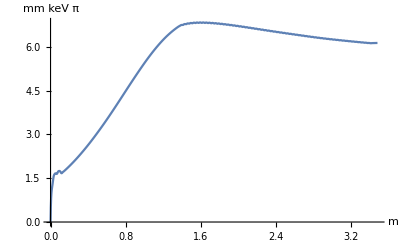

```mathematica
ListLinePlot[{Transpose[{z,ϵznorm}]},AxesLabel->Automatic]
```

```mathematica
ASTRAemitInterpret["020.Zemit.001",ASTRAVerbose->True]
```

Columns Redefined: z [Meters], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [Meters], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [Meters], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
ASTRABeamInterpret["020.0348.001",ASTRAVerbose->True]
```

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [], status []

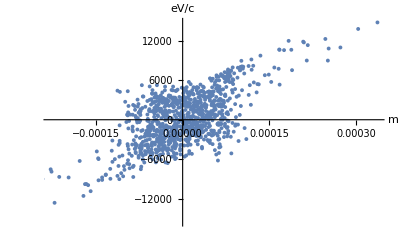

```mathematica
ListPlot[{Transpose[{x,px}][[1;;-1;;10]]},AxesLabel->Automatic]
```